# Katz mass: Is there a solution?

## The idea is to figure out the mass formula (which I do in the Jupyter doc), then put this into the Einstein Field Equations, which spit out a T tensor, and that ‘T’ represents the gravitational energy density (which should NOT be the Katz formula exactly, as we now ascribe mass to the gravitational field).

So I take an isotropic Schwarzchild, and instead of mass being a constant, I lower the mass as one approaches the horizon, we assume that the energy is given to the Gravitational Field energy  - like Katz.

## The mass formula as a function of radius was found by tom

Here is the formula from Katz - in isotropic coords, the gravitational field energy outside isotropic r is 
m^2/2r - BUT as we move in in radius, the available mass left to make the central bit drops, and thus we are left with.  So in Dec 2024, I calculated that the mass inside isotropic r decreases as  M = m - m/(1 + 2r/m) See the Jupyter doc.  I also assume Birchoff’s theorem...I numerically obtained a solution to the integral equation for Brown-York Katz gravitational energy density... Isotropic... (likely there is an analytic version).

So use this as our mass formula

```mathematica
M := m - m /(1 + 2 r/m)
```

Use the isotropic metric, but use ‘big M’ - mass as a function of r as above...

And sub it into the isotropic metric...

-Graphics-

```mathematica
pointMassMetric = ResourceFunction["MetricTensor"][{{(-(1 - M/(2 r))^2)/(1 + M/(2 r))^2,0,0,0},{0,(1 + M/(2 r))^4,0,0},{0,0,(1 + M/(2 r))^4 r^2,0},{0,0,0, (1 + M/(2 r))^4(r Sin[θ])^2}}, {t, r,θ, φ}]
```

MetricTensor[…]

The metric looks quite neat and small, actually...

```mathematica
pointMassMetric["ReducedMatrixRepresentation"] // MatrixForm
```

(-r^2/(m+r)^2 | 0 | 0 | 0
0 | (16 (m+r)^4)/(m+2 r)^4 | 0 | 0
0 | 0 | (16 r^2 (m+r)^4)/(m+2 r)^4 | 0
0 | 0 | 0 | (16 r^2 (m+r)^4 Sin[θ]^2)/(m+2 r)^4)

```mathematica
pointMassMetric["Properties"]
```

{MatrixRepresentation,ReducedMatrixRepresentation,Coordinates,CoordinateOneForms,Indices,CovariantQ,ContravariantQ,MixedQ,Symbol,Dimensions,SymmetricQ,DiagonalQ,Signature,RiemannianQ,PseudoRiemannianQ,LorentzianQ,RiemannianConditions,PseudoRiemannianConditions,LorentzianConditions,MetricSingularities,Determinant,ReducedDeterminant,Trace,ReducedTrace,Eigenvalues,ReducedEigenvalues,Eigenvectors,ReducedEigenvectors,MetricTensor,InverseMetricTensor,LineElement,ReducedLineElement,VolumeForm,ReducedVolumeForm,TimelikeQ,LightlikeQ,SpacelikeQ,LengthPureFunction,AnglePureFunction,Properties}

```mathematica
pointMassMetric["MetricSingularities"]
```

{{r→-m},{r→-m/2}}

## Einstein Tensor

```mathematica
pointMassEinsteinTensor= ResourceFunction["EinsteinTensor"][pointMassMetric]
```

EinsteinTensor[…]

```mathematica
pointMassEinsteinTensor["ReducedMatrixRepresentation"] // MatrixForm
```

((m^2 r (m+2 r)^2)/(2 (m+r)^7) | 0 | 0 | 0
0 | (2 m^3)/(r^2 (m+r) (m+2 r)^2) | 0 | 0
0 | 0 | m^3/((m+r) (m+2 r)^2) | 0
0 | 0 | 0 | (m^3 Sin[θ]^2)/((m+r) (m+2 r)^2))

Its not a vacuum solution...-- which is what I was planning, this is then the ‘Stress Energy Tensor’ which now is only built of pure gravitational field energy.  As r >> m, one gets....
, which is 2m^2/r^4, m^3/2r^5, m^3/4r^5, m^3/4r^5  (in minkowksian t, x, y, z)

```mathematica
einsteinMixedSE=ResourceFunction["EinsteinTensor"][pointMassEinsteinTensor,False,True]
```

EinsteinTensor[…]

```mathematica
einsteinMixedSE["ReducedMatrixRepresentation"] // MatrixForm
```

(-(m^2 (m+2 r)^2)/(2 r (m+r)^5) | 0 | 0 | 0
0 | (m^3 (m+2 r)^2)/(8 r^2 (m+r)^5) | 0 | 0
0 | 0 | (m^3 (m+2 r)^2)/(16 r^2 (m+r)^5) | 0
0 | 0 | 0 | (m^3 (m+2 r)^2)/(16 r^2 (m+r)^5))

```mathematica
einsteinUpperSE=pointMassEinsteinTensor["ContravariantEinsteinTensor"]
```

EinsteinTensor[…]

```mathematica
einsteinUpperSE["ReducedMatrixRepresentation"] // MatrixForm
```

((m^2 (m+2 r)^2)/(2 r^3 (m+r)^3) | 0 | 0 | 0
0 | (m^3 (m+2 r)^6)/(128 r^2 (m+r)^9) | 0 | 0
0 | 0 | (m^3 (m+2 r)^6)/(256 r^4 (m+r)^9) | 0
0 | 0 | 0 | (m^3 (m+2 r)^6 Csc[θ]^2)/(256 r^4 (m+r)^9))

Too is the lower indicies covariant upper left component... (energy density)

```mathematica
Too = (m^2 r (m+2 r)^2)/(2 (m+r)^7)
```

(m^2 r (m+2 r)^2)/(2 (m+r)^7)

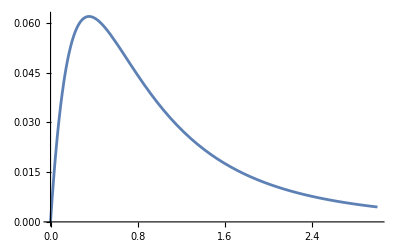

```mathematica
With[{m = 1},Plot[(m^2 r (m+2 r)^2)/(2 (m+r)^7),{r,0,3} ]]
```

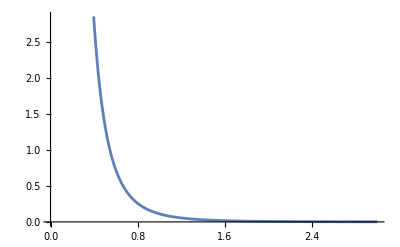

```mathematica
With[{m = 1},Plot[(2 m^3)/(r^2 (m+r) (m+2 r)^2),{r,0,3} ]]
```

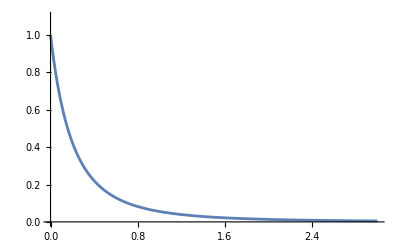

```mathematica
With[{m = 1},Plot[m^3/((m+r) (m+2 r)^2),{r,0,3}, PlotRange->{0,1.1} ]]
```

```mathematica
pointMassEinsteinTensor["Properties"]
```

{MatrixRepresentation,ReducedMatrixRepresentation,SymbolicMatrixRepresentation,Trace,ReducedTrace,SymbolicTrace,MetricTensor,Coordinates,CoordinateOneForms,Indices,CovariantQ,ContravariantQ,MixedQ,Symbol,EinsteinFlatQ,VanishingEinsteinTraceQ,EinsteinFlatConditions,VanishingEinsteinTraceCondition,CovariantDerivatives,ReducedCovariantDerivatives,SymbolicCovariantDerivatives,BianchiIdentities,SymbolicBianchiIdentities,Dimensions,SymmetricQ,DiagonalQ,Signature,RiemannianQ,PseudoRiemannianQ,LorentzianQ,RiemannianConditions,PseudoRiemannianConditions,LorentzianConditions,CurvatureSingularities,TraceSingularities,Determinant,ReducedDeterminant,SymbolicDeterminant,Eigenvalues,ReducedEigenvalues,Eigenvectors,ReducedEigenvectors,CovariantEinsteinTensor,ContravariantEinsteinTensor,Properties}

```mathematica
pointMassEinsteinTensor["ReducedTrace"]
```

(m^2 (m-2 r) (m+2 r)^2)/(4 r^2 (m+r)^5)

```mathematica
pointMassEinsteinTensor["CurvatureSingularities"]
```

{{r→0},{r→-m},{r→-m/2}}

```mathematica
pointMassEinsteinTensor["RiemannianConditions"]
```

{(m+r)^2 (m+2 r)^2>0,r^2 (m+r)^2 (m+2 r)^2>0,r^2 (m+r)^2<0,r^2 (m+r)^2 (m+2 r)^2 Sin[θ]^2>0}

```mathematica
pointMassEinsteinTensor["LorentzianConditions"]
```

{(m+r)^2 (m+2 r)^2>0,r^2 (m+r)^2 (m+2 r)^2>0,r^2 (m+r)^2>0,r^2 (m+r)^2 (m+2 r)^2 Sin[θ]^2>0}

## Ricci Tensor

```mathematica
pointMassRicciTensor= ResourceFunction["RicciTensor"][pointMassMetric]
```

RicciTensor[…]

```mathematica
pointMassRicciTensor["ReducedMatrixRepresentation"] //MatrixForm
```

((m^2 (m+2 r)^3)/(8 (m+r)^7) | 0 | 0 | 0
0 | (4 m^2)/(r (m+r) (m+2 r)^2) | 0 | 0
0 | 0 | -(m^2 (m-4 r))/((m+r) (m+2 r)^2) | 0
0 | 0 | 0 | -(m^2 (m-4 r) Sin[θ]^2)/((m+r) (m+2 r)^2))

```mathematica
pointMassRicciTensor["Properties"]
```

{MatrixRepresentation,ReducedMatrixRepresentation,SymbolicMatrixRepresentation,RicciScalar,ReducedRicciScalar,SymbolicRicciScalar,MetricTensor,Coordinates,CoordinateOneForms,Indices,CovariantQ,ContravariantQ,MixedQ,Symbol,RicciFlatQ,VanishingRicciScalarQ,RicciFlatConditions,VanishingRicciScalarCondition,CovariantDerivatives,ReducedCovariantDerivatives,SymbolicCovariantDerivatives,BianchiIdentities,SymbolicBianchiIdentities,Dimensions,SymmetricQ,DiagonalQ,Signature,RiemannianQ,PseudoRiemannianQ,LorentzianQ,RiemannianConditions,PseudoRiemannianConditions,LorentzianConditions,CurvatureSingularities,ScalarCurvatureSingularities,Determinant,ReducedDeterminant,SymbolicDeterminant,Eigenvalues,ReducedEigenvalues,Eigenvectors,ReducedEigenvectors,CovariantRicciTensor,ContravariantRicciTensor,ScalarVolumeExpansion,ReducedScalarVolumeExpansion,SymbolicScalarVolumeExpansion,VolumeFormExpansion,ReducedVolumeFormExpansion,SymbolicVolumeFormExpansion,Properties}

```mathematica
pointMassRicciTensor["ReducedRicciScalar"]
```

-(m^2 (m-2 r) (m+2 r)^2)/(4 r^2 (m+r)^5)

## RiemannTensor

```mathematica
pointMassRiemennianTensor= ResourceFunction["RiemannTensor"][pointMassMetric]
```

RiemannTensor[…]

```mathematica
pointMassRiemennianTensor["ReducedTensorRepresentation"]  // MatrixForm
```

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | (4 m)/((m+r)^2 (m+2 r)) | 0 | 0
-(4 m)/((m+r)^2 (m+2 r)) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | -(m (m^2+m r+2 r^2))/((m+r)^2 (m+2 r)) | 0
0 | 0 | 0 | 0
(m (m^2+m r+2 r^2))/((m+r)^2 (m+2 r)) | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | -(m (m^2+m r+2 r^2) Sin[θ]^2)/((m+r)^2 (m+2 r))
0 | 0 | 0 | 0
0 | 0 | 0 | 0
(m (m^2+m r+2 r^2) Sin[θ]^2)/((m+r)^2 (m+2 r)) | 0 | 0 | 0)
(0 | (m r^2 (m+2 r)^3)/(4 (m+r)^8) | 0 | 0
-(m r^2 (m+2 r)^3)/(4 (m+r)^8) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | (2 m r (m^2-2 r^2))/((m+r)^2 (m+2 r)^2) | 0
0 | (-2 m^3 r+4 m r^3)/((m+r)^2 (m+2 r)^2) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | (2 m r (m^2-2 r^2) Sin[θ]^2)/((m+r)^2 (m+2 r)^2)
0 | 0 | 0 | 0
0 | -(2 m r (m^2-2 r^2) Sin[θ]^2)/((m+r)^2 (m+2 r)^2) | 0 | 0)
(0 | 0 | -(m (m+2 r)^3 (m^2+m r+2 r^2))/(16 (m+r)^8) | 0
0 | 0 | 0 | 0
(m (m+2 r)^3 (m^2+m r+2 r^2))/(16 (m+r)^8) | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | (-2 m^3+4 m r^2)/(r (m+r)^2 (m+2 r)^2) | 0
0 | (2 (m^3-2 m r^2))/(r (m+r)^2 (m+2 r)^2) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | (4 m r (m^2+2 m r+2 r^2) Sin[θ]^2)/((m+r)^2 (m+2 r)^2)
0 | 0 | -(4 m r (m^2+2 m r+2 r^2) Sin[θ]^2)/((m+r)^2 (m+2 r)^2) | 0)
(0 | 0 | 0 | -(m (m+2 r)^3 (m^2+m r+2 r^2))/(16 (m+r)^8)
0 | 0 | 0 | 0
0 | 0 | 0 | 0
(m (m+2 r)^3 (m^2+m r+2 r^2))/(16 (m+r)^8) | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | (-2 m^3+4 m r^2)/(r (m+r)^2 (m+2 r)^2)
0 | 0 | 0 | 0
0 | (2 (m^3-2 m r^2))/(r (m+r)^2 (m+2 r)^2) | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | -(4 m r (m^2+2 m r+2 r^2))/((m+r)^2 (m+2 r)^2)
0 | 0 | (4 m r (m^2+2 m r+2 r^2))/((m+r)^2 (m+2 r)^2) | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

```mathematica
pointMassRiemennianTensor["Properties"]
```

{TensorRepresentation,ReducedTensorRepresentation,SymbolicTensorRepresentation,KretschmannScalar,ReducedKretschmannScalar,SymbolicKretschmannScalar,ChernPontryaginScalar,ReducedChernPontryaginScalar,SymbolicChernPontryaginScalar,EulerScalar,ReducedEulerScalar,SymbolicEulerScalar,MetricTensor,Coordinates,CoordinateOneForms,Indices,CovariantQ,ContravariantQ,MixedQ,Symbol,RiemannFlatQ,VanishingKretschmannScalarQ,VanishingChernPontryaginScalarQ,VanishingEulerScalarQ,RiemannFlatConditions,VanishingKretschmannScalarCondition,VanishingChernPontryaginScalarCondition,VanishingEulerScalarCondition,IndexContractions,ReducedIndexContractions,SymbolicIndexContractions,CovariantDerivatives,ReducedCovariantDerivatives,SymbolicCovariantDerivatives,BianchiIdentities,SymbolicBianchiIdentities,Dimensions,Signature,RiemannianQ,PseudoRiemannianQ,LorentzianQ,RiemannianConditions,PseudoRiemannianConditions,LorentzianConditions,CurvatureSingularities,KretschmannSingularities,ChernPontryaginSingularities,EulerSingularities,CovariantRiemannTensor,ContravariantRiemannTensor,Properties}

```mathematica
(*pointMassRiemennianTensor["ReducedKretschmannScalar"]*)
```

```mathematica
(*pointMassRiemennianTensor["ReducedEulerScalar"]*)
```

```mathematica
(*pointMassRiemennianTensor["CurvatureSingularities"]*)
```

```mathematica
(*pointMassRiemennianTensor["ReducedChernPontryaginScalar"]*)
```

## The gravitational potential of the energy - NOT infinite like a point mass...

With the energy distributed as in the equation M := m - m /(1 + 2 r/m) - what is the gravitational potential, etc?
-Graphics-

So we want to get U(R) - note that it depnds on the density interior to the radius r. 
-Graphics-

So lets integrate: (The 4pi(in the U definition)/8pi (in the densisty) almost cancel...)

```mathematica
PotE := -Integrate[M/(2 r) (M/(r^2(1 + M/(2r))^3))^2 (r^2),r]
```

```mathematica
FullSimplify[PotE]
```

(m^3 (13 m^3+55 m^2 r+80 m r^2+40 r^3))/(160 (m+r)^5)

Evaluate the integral from r = 0 to r = infinity, you get 13m/160 (i likely have some constants wrong..?)

```mathematica
PotE/. {r->0}
```

(13 m)/160

At infinity its zero... (1/r^2)

```mathematica
PotE/. {r->100000000.0, m-> 1}
```

2.5×10^-17

## OK Look at the resulting field:

We have the gravitational potential formula of Newton, and our mass formula...
Working in isotropic coords here...

```mathematica
GPot := M/r
```

```mathematica
FullSimplify[GPot]
```

(2 m)/(m+2 r)

```mathematica
gForce := D[GPot,r]
```

```mathematica
FullSimplify[gForce]
```

-(4 m)/(m+2 r)^2

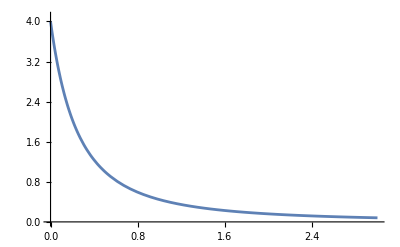

```mathematica
With[{m = 1},Plot[(4 m)/(m+2 r)^2,{r,0,3}, PlotRange->{0,4.1} ]]
```

So 1/r squared, without an infinte peak - there is no singularity.

-Graphics-

```mathematica
anomalousGForce := - m/r^2 +(4 m)/(m+2 r)^2
```

```mathematica
FullSimplify[anomalousGForce]
```

m (-1/r^2+4/(m+2 r)^2)

```mathematica
Series[m (-1/r^2+4/(m+2 r)^2),{r,Infinity,3}]
```

-m^2/r^3+O[1/r]^4

```mathematica
Together[anomalousGForce]
```

-(m^2 (m+4 r))/(r^2 (m+2 r)^2)

## Stress Energy Tensor

```mathematica
matrixSE = pointMassEinsteinTensor["ContravariantEinsteinTensor"]["ReducedMatrixRepresentation"]
```

{{(m^2 (m+2 r)^2)/(2 r^3 (m+r)^3),0,0,0},{0,(m^3 (m+2 r)^6)/(128 r^2 (m+r)^9),0,0},{0,0,(m^3 (m+2 r)^6)/(256 r^4 (m+r)^9),0},{0,0,0,(m^3 (m+2 r)^6 Csc[θ]^2)/(256 r^4 (m+r)^9)}}

```mathematica
metricContra = pointMassMetric["InverseMetricTensor"]
```

MetricTensor[…]

```mathematica
stressEnergyT= ResourceFunction["StressEnergyTensor"][matrixSE,metricContra, False, False]
```

StressEnergyTensor[…]

```mathematica
stressEnergyT["Properties"]
```

{MatrixRepresentation,ReducedMatrixRepresentation,Trace,ReducedTrace,MetricTensor,Coordinates,CoordinateOneForms,Indices,CovariantQ,ContravariantQ,MixedQ,Symbol,EnergyDensity,ReducedEnergyDensity,MomentumDensity,ReducedMomentumDensity,SpacetimeMomentumDensity,ReducedSpacetimeMomentumDensity,Pressure,ReducedPressure,StressTensor,ReducedStressTensor,ShearStressTensor,ReducedShearStressTensor,CovariantDerivatives,ReducedCovariantDerivatives,SymbolicCovariantDerivatives,ContinuityEquations,ReducedContinuityEquations,SymbolicContinuityEquations,Dimensions,SymmetricQ,DiagonalQ,Signature,RiemannianQ,PseudoRiemannianQ,LorentzianQ,RiemannianConditions,PseudoRiemannianConditions,LorentzianConditions,StressEnergySingularities,TraceSingularities,Determinant,ReducedDeterminant,Eigenvalues,ReducedEigenvalues,Eigenvectors,ReducedEigenvectors,CovariantStressEnergyTensor,ContravariantStressEnergyTensor,NullEnergyCondition,ReducedNullEnergyCondition,WeakEnergyCondition,ReducedWeakEnergyCondition,DominantEnergyCondition,ReducedDominantEnergyCondition,StrongEnergyCondition,ReducedStrongEnergyCondition,Properties}

```mathematica
stressEnergyT["ReducedMatrixRepresentation"]//MatrixForm
```

((m^2 (m+2 r)^2)/(2 r^3 (m+r)^3) | 0 | 0 | 0
0 | (m^3 (m+2 r)^6)/(128 r^2 (m+r)^9) | 0 | 0
0 | 0 | (m^3 (m+2 r)^6)/(256 r^4 (m+r)^9) | 0
0 | 0 | 0 | (m^3 (m+2 r)^6 Csc[θ]^2)/(256 r^4 (m+r)^9))

```mathematica
stressEnergyT["ReducedPressure"]
```

(m^3 (m+2 r)^6 (1+2 r^2+Csc[θ]^2))/(768 r^4 (m+r)^9)

```mathematica
stressEnergyT["ReducedMomentumDensity"]
```

{0,0,0}

```mathematica
stressEnergyT["ReducedSpacetimeMomentumDensity"]
```

{(m^2 (m+2 r)^2)/(2 r^3 (m+r)^3),0,0,0}

```mathematica
stressEnergyT["EnergyDensity"]
```

(m^2 (m+2 r)^2)/(2 r^3 (m+r)^3)

```mathematica
stressEnergyT["ReducedStrongEnergyCondition"]
```

16 (m+r)^8 (m+2 r)^2 ((X^2)^2+r^2 ((X^3)^2+Sin[θ]^2 (X^4)^2))<r^2 (m+r)^2 (m+2 r)^6 (X^1)^2⇒(m^2 (128 r (m+r)^6 (m+2 r)^4 (-m^5-2 m^4 r+4 m^3 r^2+8 m^2 r^3+8 m r^6+8 r^7) (X^1)^2+2 m r^2 (2048 r^2 (m+r)^13-m^2 (m-2 r) (m+2 r)^10) (X^2)^2+m (2048 r^6 (m+r)^13-m^2 (m-2 r) (m+2 r)^10) (X^3)^2-m (-2048 r^6 (m+r)^13+m^2 (m-2 r) (m+2 r)^10 Csc[θ]^4) Sin[θ]^2 (X^4)^2))/(2048 r^6 (m+r)^14 (m+2 r)^2)≥0

```mathematica
stressEnergyT["ReducedDominantEnergyCondition"]
```

16 (m+r)^8 (m+2 r)^2 ((X^2)^2+r^2 ((X^3)^2+Sin[θ]^2 (X^4)^2))<r^2 (m+r)^2 (m+2 r)^6 (X^1)^2⇒(m^2 r (m+2 r)^2 (X^1)^2)/(m+r)+(2 m^3 (m+r)^5 (2 (X^2)^2+r^2 ((X^3)^2+Sin[θ]^2 (X^4)^2)))/(r^2 (m+2 r)^2)≥0&&(m^4 (m+r)^4 (4 (X^2)^2+r^2 ((X^3)^2+Sin[θ]^2 (X^4)^2)))/r^2≤(4 m^2 r^2 (m+2 r)^4 (X^1)^2)/(m+r)^2